```mathematica
ClearAll["Global`*"]
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
data = Import[NotebookDirectory[]<>"SpherePlaneResistance.txt","Table"];
ξdata=data[[All,1]];
XAdata=data[[All,2]];
YAdata=data[[All,3]];
YBdata=data[[All,4]];
XCdata=data[[All,5]];
YCdata=data[[All,6]];
δ=0.01;
YAVal=Interpolation[Transpose[{ξdata,YAdata}]][δ];
YBVal=Interpolation[Transpose[{ξdata,YBdata}]][δ];
YCVal=Interpolation[Transpose[{ξdata,YCdata}]][δ];
XAVal=Interpolation[Transpose[{ξdata,XAdata}]][δ];
XCVal=Interpolation[Transpose[{ξdata,XCdata}]][δ];
AA={{YAVal,0,0},{0,YAVal,0},{0,0,XAVal}};
BB={{0,YBVal,0},{-YBVal,0,0},{0,0,0}};
CC={{YCVal,0,0},{0,YCVal,0},{0,0,XCVal}};
Resistance=ArrayFlatten[ {{AA,Transpose[BB]},{BB,CC}}];
```

```mathematica
TrigReduce[Cos[0.3 t] Sin[0.03 t]]
```

1/2 (-Sin[(0.27+0. ⅈ) t]+Sin[(0.33+0. ⅈ) t])

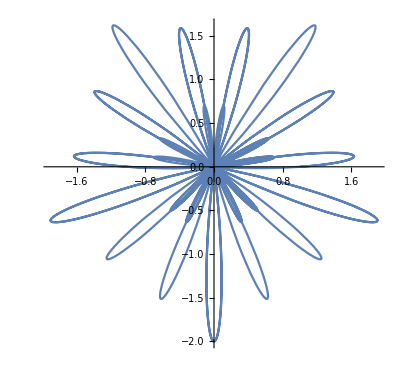

```mathematica
ParametricPlot[{(Cos[0.2 t ]+Sin[0.3 t]) Cos[0.02t],(Cos[0.2 t ]+Sin[0.3 t]) Sin[0.02 t] },{t,0,500}]
```

```mathematica
B[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_},t_]:={B1 Cos[(ω1-ω4)t]+B2 Cos[(ω1+ω4) t],-B1 Sin[(ω1-ω4) t]+B2 Sin[(ω1+ω4) t], (A1 Sin[t ω1 ]+A2*Sin[ω2 t ]+A3 Sin[ω3 t])}.RotationMatrix[10 Degree ,{0,1,0}];

Bflat[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_},t_]:={B1 Cos[(ω1-ω4)t]+B2 Cos[(ω1+ω4) t],-B1 Sin[(ω1-ω4) t]+B2 Sin[(ω1+ω4) t], (A1 Sin[t ω1 ]+A2*Sin[ω2 t ]+A3 Sin[ω3 t])};

roller[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_}]:=Module[{parameter,tMax,Rq,mq,Lq,F,FLq,UΩq,Uq,Ωq,Q,quaternionRate,
q,ϕ,θ,ψ,qIC,para,sol,data,dct,tdata},
parameter={ω1,ω2,ω3,ω4,A1,A2,A3,B1,B2};
tMax = (*Min[200 2 π/parameter[[1]],50000.0]*0+*)5000;
(*first field is magnetic , second is gravity*)

Rq={{q0^2+q1^2-q2^2-q3^2,2q1 q2+2q0 q3,2q1 q3-2q0 q2},
{2q1 q2-2q0 q3,q0^2-q1^2+q2^2-q3^2,2q2 q3+2q0 q1},
{2 q1 q3+2 q0 q2,2q2 q3-2 q0 q1, q0^2-q1^2-q2^2+q3^2}};
(*magnetic moment*)
mq=Simplify[Transpose[Rq] .{0,0,1}   ];
Lq=Simplify[Cross[mq,B[parameter,t    ]   ]];
(*force *)
F ={0 ,0,0};
FLq=ArrayFlatten[{F,Lq},1];
UΩq=Simplify[Inverse[Resistance].FLq];
Uq=UΩq[[1;;3]];
Ωq=UΩq[[4;;6]];
Q ={{q0 ,-q1,-q2,-q3},
{q1,q0,q3,-q2},
{q2,-q3,q0,q1},
{q3,q2,-q1,q0}};
(*equation 156*)
quaternionRate=1/2 Q.ArrayFlatten[{{0},Ωq},1];
q={Cos[ϕ/2]Cos[θ/2]Cos[ψ/2]-Sin[ϕ/2]Cos[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Sin[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2],
Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]+Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]};
qIC = q/.{ϕ->RandomReal[2 π],θ->RandomReal[2 π],ψ->RandomReal[2 π]};
para={q0->q0[t],q1->q1[t],q2->q2[t],q3->q3[t]};
sol=NDSolve[{
q0'[t]==(quaternionRate[[1]]/.para),
q1'[t]==(quaternionRate[[2]]/.para),
q2'[t]==(quaternionRate[[3]]/.para),
q3'[t]==(quaternionRate[[4]]/.para),
x'[t]==(Uq[[1]]/.para),
y'[t]==(Uq[[2]]/.para),
q0[0]==qIC[[1]],
q1[0]==qIC[[2]],
q2[0]==qIC[[3]],
q3[0]==qIC[[4]],
x[0]==0,
y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},{t,0,tMax}];
(*data=Table[x[t]/.sol[[1]],{t,0,4000,1}];
dct=FourierDCT[data];
  tdata=FourierDCT[PadRight[Take[dct,2],4000,0],3];*)
(*Mean[D[y[t]/.sol[[1]],t]/.t->Table[i,{i,tMax 0.5,tMax}]]*)
(*y[t]/.sol[[1]]/.t->Table[i,{i,200 2 π/ω1 0.5,200 2 π/ω1 0.75,1}];
200 2 π/ω1 0.75*)
(*data1=Table[{t/(  2 π/ω2),x[t]/.sol[[1]]},{t,0,4000,1}];
data2=Table[{t/(2 π /ω2),y[t]/.sol[[1]]},{t,0,4000,1}];
lm1=LinearModelFit[MovingAverage[data1,Round[      2 π/ω2]],x,x];
lm2=LinearModelFit[MovingAverage[data2,Round[      2 π/ω2]],x,x];
{sol,lm1["BestFitParameters"][[2]],lm2["BestFitParameters"][[2]]}*)
sol
]
rollerflat[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_}]:=Module[{parameter,tMax,Rq,mq,Lq,F,FLq,UΩq,Uq,Ωq,Q,quaternionRate,
q,ϕ,θ,ψ,qIC,para,sol,data,dct,tdata},
parameter={ω1,ω2,ω3,ω4,A1,A2,A3,B1,B2};
tMax =(* Min[200 2 π/parameter[[1]],50000.0]+*)5000;
(*first field is magnetic , second is gravity*)

Rq={{q0^2+q1^2-q2^2-q3^2,2q1 q2+2q0 q3,2q1 q3-2q0 q2},
{2q1 q2-2q0 q3,q0^2-q1^2+q2^2-q3^2,2q2 q3+2q0 q1},
{2 q1 q3+2 q0 q2,2q2 q3-2 q0 q1, q0^2-q1^2-q2^2+q3^2}};
(*magnetic moment*)
mq=Simplify[Transpose[Rq] .{0,0,1}   ];
Lq=Simplify[Cross[mq,Bflat[parameter,t    ]   ]];
(*force *)
F ={0 ,0,0};
FLq=ArrayFlatten[{F,Lq},1];
UΩq=Simplify[Inverse[Resistance].FLq];
Uq=UΩq[[1;;3]];
Ωq=UΩq[[4;;6]];
Q ={{q0 ,-q1,-q2,-q3},
{q1,q0,q3,-q2},
{q2,-q3,q0,q1},
{q3,q2,-q1,q0}};
(*equation 156*)
quaternionRate=1/2 Q.ArrayFlatten[{{0},Ωq},1];
q={Cos[ϕ/2]Cos[θ/2]Cos[ψ/2]-Sin[ϕ/2]Cos[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Sin[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2],
Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]+Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]};
qIC = q/.{ϕ->RandomReal[2 π],θ->RandomReal[2 π],ψ->RandomReal[2 π]};
para={q0->q0[t],q1->q1[t],q2->q2[t],q3->q3[t]};
sol=NDSolve[{
q0'[t]==(quaternionRate[[1]]/.para),
q1'[t]==(quaternionRate[[2]]/.para),
q2'[t]==(quaternionRate[[3]]/.para),
q3'[t]==(quaternionRate[[4]]/.para),
x'[t]==(Uq[[1]]/.para),
y'[t]==(Uq[[2]]/.para),
q0[0]==qIC[[1]],
q1[0]==qIC[[2]],
q2[0]==qIC[[3]],
q3[0]==qIC[[4]],
x[0]==0,
y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},{t,0,tMax}];
(*data=Table[x[t]/.sol[[1]],{t,0,4000,1}];
dct=FourierDCT[data];
  tdata=FourierDCT[PadRight[Take[dct,2],4000,0],3];*)
(*Mean[D[y[t]/.sol[[1]],t]/.t->Table[i,{i,tMax 0.5,tMax}]]*)
(*y[t]/.sol[[1]]/.t->Table[i,{i,200 2 π/ω1 0.5,200 2 π/ω1 0.75,1}];
200 2 π/ω1 0.75*)
(*data1=Table[{t/(  2 π/ω2),x[t]/.sol[[1]]},{t,0,4000,1}];
data2=Table[{t/(2 π /ω2),y[t]/.sol[[1]]},{t,0,4000,1}];
lm1=LinearModelFit[MovingAverage[data1,Round[      2 π/ω2]],x,x];
lm2=LinearModelFit[MovingAverage[data2,Round[      2 π/ω2]],x,x];
{sol,lm1["BestFitParameters"][[2]],lm2["BestFitParameters"][[2]]}*)
sol
]


(*B[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_},t_]*)
```

```mathematica
(*ω1=0.3;
ω2=0.3 2;
ω3=0.3*3;
ω4=0.01;
A1=1/10 4;
A2=-1/10 0;
A3=1/15 0;
B1=0.5;
B2=0.8;*)
can={};
For [i=0,i<1000,
ω1=RandomReal[];
ω2=RandomReal[{ω1,1}];
ω3=RandomReal[{ω2,2}];
ω4=ω1/RandomReal[{10,30}];
A1=RandomReal[{-2,2}];
A2=RandomReal[{-2,2}];
A3=RandomReal[{-2,2}];
B1=RandomReal[{-2,2}];
B2=RandomReal[{-2,2}];
sol1=roller[{ω1,ω2,ω3,ω4,A1,A2,A3,B1, B2}];
sol2=rollerflat[{ω1,ω2,ω3,ω4,A1,A2,A3,B1, B2}];
bias=Table[x[t]/.sol1[[1]],{t,1,5000}];
flat=Table[x[t]/.sol2[[1]],{t,1,5000}];
If[(Min[flat]-Min[bias]>1)&&(Abs[Min[bias]/(y[t]/.sol1[[1]]/.t->Ordering[bias,1][[1]])]>0.36), can =Append[can,{ω1,ω2,ω3,ω4,A1,A2,A3,B1, B2}]];
i++
]
```

```mathematica
Length[can]
```

31

12.8481

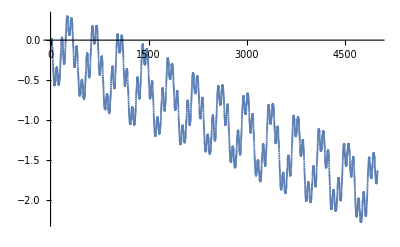

```mathematica
ListPlot[flat]
```

```mathematica
can
```

{{0.26323,0.197787,0.298471,0.0162171,0.339649,-0.822587,-0.0467963,0.218119,0.734976}}

{s,s}

{0.60016,0.771967,1.85059,0.037715,-1.22243,-0.689366,-1.75521,1.15597,-0.98458}

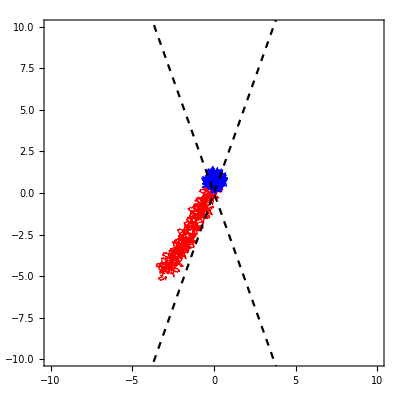

```mathematica
para=can[[31]]
sol1=roller[para];
sol2=rollerflat[para];
Show[
ParametricPlot[{x[t]/.sol1[[1]],y[t]/.sol1[[1]]},{t,0,5000},PlotStyle->{Red, AbsoluteThickness[0.9]},PlotRange->{{-10,10},{-10,10}},Frame->True,Axes->False],
ParametricPlot[{x[t]/.sol2[[1]],y[t]/.sol2[[1]]},{t,0,5000},PlotStyle->{Blue, AbsoluteThickness[0.9]},PlotRange->{{-10,10},{-10,10}},Frame->True,Axes->False],
Plot[{Cot[20 Degree]x,-Cot[20 Degree]x},{x,-10,10},PlotStyle->{{Dashed,Black},{Dashed,Black}}]

]
```

```mathematica
{0.511610972251507,0.7908980392500011,0.9721937181040985,0.018303814988236116,-0.27558310463922453,0.007526608200789653,0.06897963832795106,-1.1096269873188795,-1.4979572111557324}
{0.39859712394766467,0.8607168863918295,1.7278476465778532,0.024705120822783744,-1.2558116633752618,0.20252956189596905,0.538724095484044,-1.8114032332428236,1.5467867964174156}
{0.22272351952344738,0.49288878810513426,1.3037749920984014,0.00789072745510509,0.6203495147927427,-0.10112801538776939,0.13715645840070234,-1.0650775774045247,1.278802534665049}
{0.8987293631362272,0.8992856867416452,1.9894785718132257,0.04032210061634197,-0.5123824012300604,1.4572616828271974,0.2065386736684971,-0.5321033834238946,1.4283504730250112}
{0.5506715351050331,0.6769108997036125,1.181507732455538,0.043383079371929534,1.359961102918521,0.3424199393397105,0.9180743062788626,0.515014408989618,0.45261946798316277}
{0.5524542179931413,0.5634152402708117,1.2807348538277772,0.04045851258450883,-0.3655739675164691,-0.34883393339312274,1.384467536877187,1.104719814482154,-1.0259339528382831}
{0.8261885297059393,0.8545654321715443,1.2791791925795886,0.08065546041601698,0.19363201394277763,0.15788675810826014,1.454614447449753,1.4216070184349272,-1.3321446488805284}
{0.23535917333867573,0.6747913918681565,1.6769028296071453,0.009862173339636805,0.23193006115939507,-0.06605338562371799,0.5249007330083542,1.433849950902343,1.2884689653597299}
```

```mathematica
Pick[can[[2]],{1,1,1,0,1,1,1,0,0},1]
```

{0.114839,0.547198,0.704085,-0.317738,0.0414221,0.144293}

```mathematica
can[[2]][[1;;3]]
```

{0.114839,0.547198,0.704085}

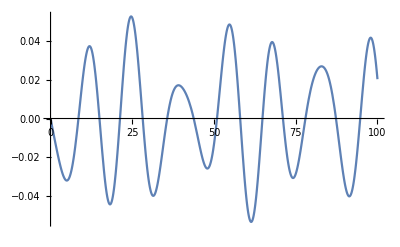

```mathematica
zfield[{ω1_,ω2_,ω3_,A1_,A2_,A3_},t_]:=A1 Sin[ω1 t ]+A2 Sin[ω2 t ]+A3 Sin[ω3 t ]
Plot[zfield[Pick[can[[11]],{1,1,1,0,1,1,1,0,0},1],t],{t,0,100}]
```